```mathematica
(*Defining all of the relevant quantities for the clade number basis *)

(* Module to calculate the mean of statistic represented by clade-number basis with representation f[n,r] *)
MeanCladeStatistic[stat_,n_]:=Module[{sum,final},sum=Sum[stat[n,r]*2 n/(r (r+1)),{r,2,n-1}];
final=sum+stat[n,n];
FullSimplify[final,Assumptions->{n>3,n∈Integers}]]
```

```mathematica
(* Defining statistic representations for all statistics represented by clade-number basis *)
sackin[n_,r_] := r;
averageLeafDepth[n_,r_]:= r/n;
totalCophenetic[n_,r_]:=Piecewise[{{Binomial[r,2], r < n},{0,r == n}}];
sHat[n_,r_] :=Log[r-1];
quadraticColless[n_,r_]:= Piecewise[{{r^2, r < n}, {2n-n^2, r==n}}];
tIPL[n_,r_]:=Piecewise[{{r, r<n}, {2-n, r == n}}];
tPL[n_,r_]:=Piecewise[{{2r, r < n}, {2, r==n}}];
aVD[n_,r_]:=Piecewise[{{2r/(2n-1), r < n}, {2/(2n-1), r == n}}];
```

2 n (-1+HarmonicNumber[n])

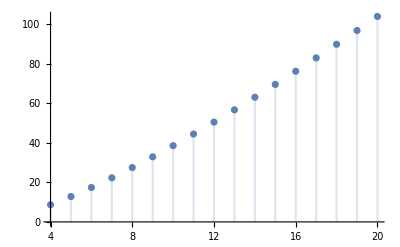

```mathematica
(* Calculating the mean in as simple of a formula as possible, for each statistic represented by clade-number basis *)
(* Sackin index *)
meanSackin = MeanCladeStatistic[sackin, n]
DiscretePlot[meanSackin, {n, 4, 20}]
```

-2+2 HarmonicNumber[n]

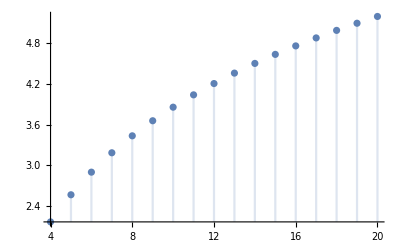

```mathematica
meanAverageLeafDepth = MeanCladeStatistic[averageLeafDepth, n]
DiscretePlot[meanAverageLeafDepth, {n, 4, 20}]
```

n (1+n-2 HarmonicNumber[n])

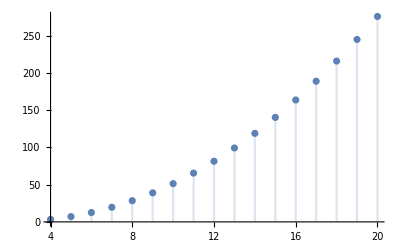

```mathematica
meanTotalCophenetic = MeanCladeStatistic[totalCophenetic,n]
DiscretePlot[meanTotalCophenetic, {n, 4, 20}]
```

Log[-1+n]+∑_(r=2)^(-1+n) (2 n Log[-1+r])/(r (1+r))

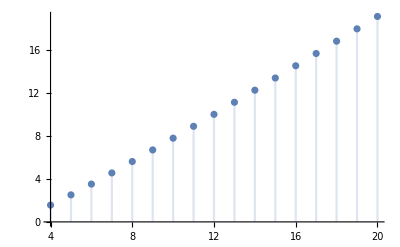

```mathematica
meanSHat = MeanCladeStatistic[sHat, n]
DiscretePlot[meanSHat, {n, 4, 20}]
```

```mathematica
meanQuadraticColless = MeanCladeStatistic[quadraticColless, n]
DiscretePlot[meanQuadraticColless, {n, 4, 20}]
```

n (1+n-2 HarmonicNumber[n])

-Graphics-

2-4 n+2 n HarmonicNumber[n]

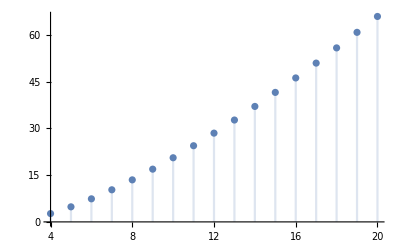

```mathematica
meanTIPL = MeanCladeStatistic[tIPL, n]
DiscretePlot[meanTIPL, {n, 4, 20}]
```

2-6 n+4 n HarmonicNumber[n]

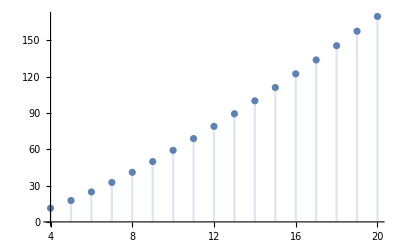

```mathematica
meanTPL = MeanCladeStatistic[tPL, n]
DiscretePlot[meanTPL, {n, 4, 20}]
```

(2-6 n+4 n HarmonicNumber[n])/(-1+2 n)

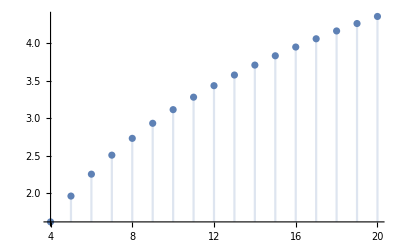

```mathematica
meanAVD = MeanCladeStatistic[aVD, n]
DiscretePlot[meanAVD, {n, 4, 20}]
```

```mathematica
(* Function to solve mean for statistics represented by daughter-number basis *)
(* Sum p_k(i) * stat[n, i, j] over a level set i + j = k; split into k even and k odd *)
PartialSumEvenK[stat_, n_, k_] := Simplify[Sum[stat[n,i, k-i] * 2/(k-1), {i, 1, k/2 - 1}] + stat[n, k/2, k/2] /(k-1), Assumptions->{n>3,n∈Integers, 2 <= k <= n, Mod[k, 2]==0}];
PartialSumOddK[stat_, n_,k_]:= Simplify[Sum[stat[n,i, k-i] * 2/(k-1), {i, 1, (k-1)/2 }], Assumptions->{n>3,n∈Integers, 2 <= k <= n, Mod[k, 2]==1}];

(* Now sum M(n,k) * Partial Sum over k=2,...,n, splitting into even and odd n cases. k0=2 is the default*)
MeanStatEvenN[stat_, n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 2, n-2, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 3, n-1, 2}] 
+ PartialSumEvenK[stat, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==0}];
MeanStatOddN[stat_, n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 2, n-1, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 3, n-2, 2}] 
+ PartialSumOddK[stat, n, n], 
Assumptions -> {n>3,n∈Integers, Mod[n, 2]==1}];

(* Aggregate into a final function *)
(* Simplify in a way that chooses a form involving HarmonicNumber instead of PolyGamma functions *)
simpHarmonic=FullSimplify[#,ComplexityFunction->(LeafCount[#]+100Count[#,_PolyGamma,All]&)]&;

MeanDaughterStatistic[stat_, n_] := simpHarmonic[Piecewise[{{MeanStatEvenN[stat, n], Mod[n,2] == 0}, {MeanStatOddN[stat, n], Mod[n,2] == 1}}], Assumptions -> {n>3,n∈Integers}];
```

```mathematica
(* Representations of indices represented by the daughter-number basis *)
colless[n_,i_,j_]:= j-i;
correctedColless[n_,i_,j_]:=2(j-i)/(n-1)/(n-2);
i2[n_,i_,j_]:=Piecewise[{{(j-i)/((n-2)(i+j-2)), i+j > 2}, {0, i+j == 2}}];
totalI[n_,i_,j_]:=(j - Floor[(i+j)/2])/((i+j-1) - Floor[(i+j)/2]); (* 0 when i + j < 4; use modified function *)
totalIPrime[n_,i_,j_]:=Piecewise[{{(j - Floor[(i+j)/2])/((i+j-1) - Floor[(i+j)/2]), EvenQ[i+j]}, {(i+j - 1)/(i+j)*(j - Floor[(i+j)/2])/((i+j-1) - Floor[(i+j)/2]), Not[EvenQ[i+j]]} }];(* 0 when i + j < 4; use modified function *)
rogersJ[n_,i_,j_]:=Piecewise[{{1, i != j}, {0, i == j}}];
rQIB[n_,i_,j_]:=Binomial[i,2]*Binomial[j,2];
stairs1[n_,i_,j_]:=Piecewise[{{1/(n-1), i != j}, {0, i == j}}];
stairs2[n_,i_,j_]:=i/j/(n-1);
```

Piecewise[{{n (-1+HarmonicNumber[n/2]), Mod[n,2]==0}, {1-n+n HarmonicNumber[1/2 (-1+n)], Mod[n,2]==1}, {0, True}}]

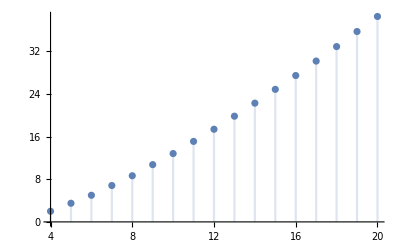

```mathematica
(* Calculating mean of each index represented by daughter-number basis *)
collessMean = MeanDaughterStatistic[colless, n]
DiscretePlot[collessMean, {n, 4, 20}]
```

Piecewise[{{(2 n (-1+HarmonicNumber[n/2]))/((-2+n) (-1+n)), Mod[n,2]==0}, {(2 (1-n+n HarmonicNumber[1/2 (-1+n)]))/((-2+n) (-1+n)), Mod[n,2]==1}, {0, True}}]

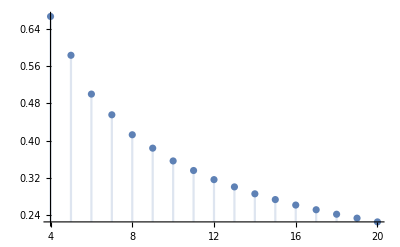

```mathematica
correctedCollessMean = MeanDaughterStatistic[correctedColless, n]
DiscretePlot[correctedCollessMean, {n, 4, 20}]
```

Piecewise[{{(n (2+3/(-1+n)+2 HarmonicNumber[1/2 (-3+n)]-2 HarmonicNumber[n/2]+Log[16]))/(6 (-2+n)), Mod[n,2]==0}, {(3+n (-1+2 n)+2 (-2+n) n (HarmonicNumber[1/2 (-4+n)]-HarmonicNumber[1/2 (-1+n)]+Log[4]))/(6 (-2+n)^2), Mod[n,2]==1}, {0, True}}]

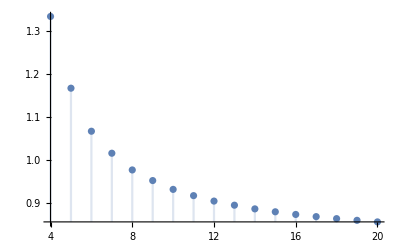

```mathematica
i2Mean = MeanDaughterStatistic[i2, n]
DiscretePlot[i2Mean, {n, 4, 20}]
```

```mathematica
(* By hand, I simplified this into a more compact expression *)
i2MeanSimplified = Piecewise[{{n/6/(n-2) * (2 + 4(HarmonicNumber[n] - HarmonicNumber[n/2]) - 1/(n-1)), Mod[n,2]==0}, {n/6/(n-2) * (2 + 4(HarmonicNumber[n-1] - HarmonicNumber[(n-1)/2]) + (3-n)/n/(n-2)), Mod[n,2]==1}}]
DiscretePlot[i2MeanSimplified, {n, 4, 20}]
```

Piecewise[{{(n (2-1/(-1+n)+4 (-HarmonicNumber[n/2]+HarmonicNumber[n])))/(6 (-2+n)), Mod[n,2]==0}, {(n (2+(3-n)/((-2+n) n)+4 (-HarmonicNumber[1/2 (-1+n)]+HarmonicNumber[-1+n])))/(6 (-2+n)), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[i2Mean==i2MeanSimplified, Assumptions->{n>3,n∈Integers}]
```

True

Piecewise[{{1/2 n (2+HarmonicNumber[1/2 (-2+n)]-HarmonicNumber[1/2 (-1+n)]-Log[4]), Mod[n,2]==0}, {1/(-1+n)+n+1/2 n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[1/2 (-2+n)]-2 Log[2]), Mod[n,2]==1}, {0, True}}]

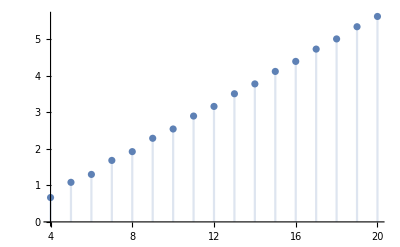

```mathematica
(* For total I, we write slightly modified functions because it is 0 for k < 4 *)
modifiedMeanStatEvenN[stat_,n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 4, n-2, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 5, n-1, 2}] 
+ PartialSumEvenK[stat, n, n], 
Assumptions -> {n>5,n∈Integers, Mod[n, 2]==0}];
modifiedMeanStatOddN[stat_, n_] := Simplify[Sum[2n/(k(k+1)) * PartialSumEvenK[stat, n,k], {k, 4, n-1, 2}]
+ Sum[2n/(k(k+1))*PartialSumOddK[stat, n, k], {k, 5, n-2, 2}] 
+ PartialSumOddK[stat, n, n], 
Assumptions -> {n>5,n∈Integers, Mod[n, 2]==1}];
modifiedMeanDaughterStatistic[stat_,n_]:=simpHarmonic[Piecewise[{{modifiedMeanStatEvenN[stat, n], Mod[n,2] == 0}, {modifiedMeanStatOddN[stat, n], Mod[n,2] == 1}}], Assumptions -> {n>5,n∈Integers}];

totalIMean = modifiedMeanDaughterStatistic[totalI, n]
DiscretePlot[totalIMean, {n, 4, 20}]
```

```mathematica
(* Using the above, I simplified the formula further by hand *)
totalIMeanSimplified = Piecewise[{{n(HarmonicNumber[n/2 - 1] - HarmonicNumber[n-1] + 1), Mod[n,2]==0}, {n(HarmonicNumber[(n-1)/2] - HarmonicNumber[n-1] + 1) - 1, Mod[n,2]==1}}]
DiscretePlot[totalIMeanSimplified, {n, 4, 20}]
```

Piecewise[{{n (1+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]), Mod[n,2]==0}, {-1+n (1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[-1+n]), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[totalIMean ==totalIMeanSimplified, Assumptions->{n>3, n∈Integers}]
```

True

Piecewise[{{1/72 (36-20 n+9 n π^2+36 n HarmonicNumber[1/2 (-2+n)]-18 n (2 HarmonicNumber[1/2 (-1+n)]+Log[16]+PolyGamma[1,(1+n)/2])), Mod[n,2]==0}, {1/72 (36+36/n-20 n+9 n π^2+36 n HarmonicNumber[1/2 (-1+n)]-18 n (2 HarmonicNumber[n/2]+Log[16]+PolyGamma[1,n/2])), Mod[n,2]==1}, {0, True}}]

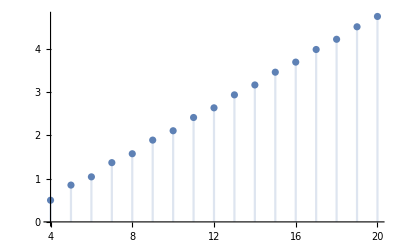

```mathematica
totalIPrimeMean = modifiedMeanDaughterStatistic[totalIPrime, n]
DiscretePlot[totalIPrimeMean, {n, 4, 20}]
```

```mathematica
(* I simplified the above formula by hand *)
totalIPrimeMeanSimplified = Piecewise[{{1/2  + n(HarmonicNumber[n/2 - 1] - HarmonicNumber[n-1] + HarmonicNumber[n-1,2] - HarmonicNumber[n/2 - 1, 2]/4 - 5/18), Mod[n,2]==0}, {1/2 + n(HarmonicNumber[(n-1)/2] - HarmonicNumber[n] + HarmonicNumber[n-1,2] - HarmonicNumber[(n-1)/2, 2]/4 - 5/18 + 1/2/n^2), Mod[n,2]==1}}]
DiscretePlot[totalIPrimeMeanSimplified, {n, 4, 20}]
```

Piecewise[{{1/2+n (-5/18+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]-1/4 HarmonicNumber[-1+n/2,2]+HarmonicNumber[-1+n,2]), Mod[n,2]==0}, {1/2+n (-5/18+1/(2 n^2)+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[n]-1/4 HarmonicNumber[1/2 (-1+n),2]+HarmonicNumber[-1+n,2]), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[totalIPrimeMean == totalIPrimeMeanSimplified, Assumptions->{n>3,n∈Integers}]
```

True

Piecewise[{{n (2-2/(-1+n)-HarmonicNumber[1/2 (-3+n)]+HarmonicNumber[1/2 (-2+n)]-Log[4]), Mod[n,2]==0}, {-2-n HarmonicNumber[1/2 (-2+n)]+n HarmonicNumber[1/2 (-1+n)]-n (-2+Log[4]), Mod[n,2]==1}, {0, True}}]

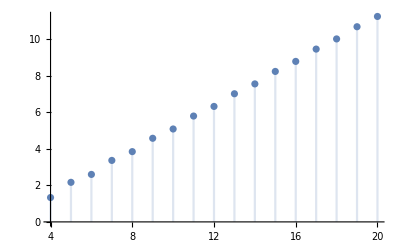

```mathematica
rogersJMean = MeanDaughterStatistic[rogersJ, n]
DiscretePlot[rogersJMean, {n, 4, 20}]
```

```mathematica
(* Computed simplified equation by hand *)
rogersJMeanSimplified = Piecewise[{{2n(HarmonicNumber[n/2 - 1] - HarmonicNumber[n-1] + 1), Mod[n,2]==0},{2n(HarmonicNumber[(n-1)/2] - HarmonicNumber[n-1] + 1) - 2, Mod[n,2]==1}}]
DiscretePlot[rogersJMeanSimplified, {n, 4, 20}]
```

Piecewise[{{2 n (1+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]), Mod[n,2]==0}, {-2+2 n (1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[-1+n]), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[rogersJMean==rogersJMeanSimplified, Assumptions->{n>3, n∈Integers}]
```

True

Piecewise[{{1/72 (-3+n) (-2+n) (-1+n) n, Mod[n,2]==0||Mod[n,2]==1}, {0, True}}]

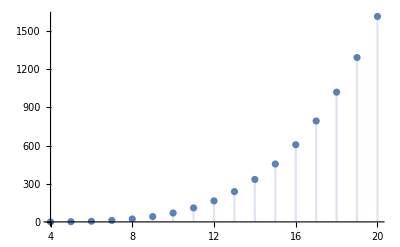

```mathematica
rQIBMean = MeanDaughterStatistic[rQIB, n]
DiscretePlot[rQIBMean, {n, 4, 20}]
```

Piecewise[{{(n (-4-(-1+n) HarmonicNumber[1/2 (-3+n)]+(-1+n) HarmonicNumber[1/2 (-2+n)]-n (-2+Log[4])+Log[4]))/(-1+n)^2, Mod[n,2]==0}, {(-2-n HarmonicNumber[1/2 (-2+n)]+n HarmonicNumber[1/2 (-1+n)]-n (-2+Log[4]))/(-1+n), Mod[n,2]==1}, {0, True}}]

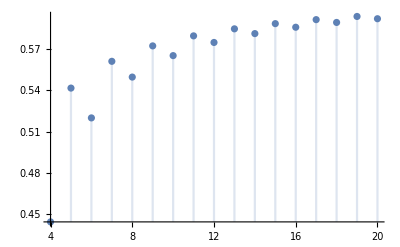

```mathematica
stairs1Mean = MeanDaughterStatistic[stairs1, n]
DiscretePlot[stairs1Mean, {n, 4, 20}]
```

```mathematica
(* Because stairs1 is just RogersJ / (n-1), we can readily use that representation for this index *)
stairs1MeanSimplified = PiecewiseExpand[1/(n-1) * rogersJMeanSimplified]
DiscretePlot[stairs1MeanSimplified, {n, 4, 20}]
```

Piecewise[{{(2 n (1+HarmonicNumber[-1+n/2]-HarmonicNumber[-1+n]))/(-1+n), Mod[n,2]==0}, {(-2+2 n (1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[-1+n]))/(-1+n), Mod[n,2]==1}, {0, True}}]

-Graphics-

```mathematica
FullSimplify[stairs1Mean == stairs1MeanSimplified, Assumptions->{n>3,n∈Integers}]
```

True

```mathematica
Clear[stairs2Mean]
```

$Aborted

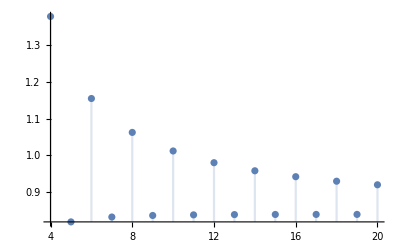

```mathematica
(* stairs2 did not simplify well using function the other ones used. Because it is more function of i and j than i + j, we will sum over j and then i instead of i+j = k *)
stairs2JSum[n_,i_]:= Simplify[2n/(2i(2i + 1)) * 1/(2i - 1) * 1/(n-1) + Sum[2n/((i+j)(i+j+1)) * 2/(i+j -1) * i/j/(n-1), {j, i+1, n-i-1} ] + 1* 1/(n-1) * i/(n-i), Assumptions->{1 <= i < n/2 && n∈Integers && i∈Integers && n>3}];

meanStairs2EvenN[n_]:= Simplify[ Sum[stairs2JSum[n,i], {i, 1, n/2}] + 1/(n-1), Assumptions->{n∈Integers, n>3, Mod[n,2]==0 }];
meanStairs2OddN[n_]:=Simplify[Sum[stairs2JSum[n,i], {i, 1, (n-1)/2}], Assumptions->{n∈Integers, n>3, Mod[n,2]==1 }];

stairs2Mean[n_]:=FullSimplify[Piecewise[{{meanStairs2EvenN[n],Mod[n,2]==0},{meanStairs2OddN[n],Mod[n,2] == 1}}], Assumptions->{n∈Integers, n>3}]
stairs2Mean[n]
DiscretePlot[stairs2Mean[n], {n, 4, 20}]
```

Piecewise[{{(2 (1+n) (HarmonicNumber[-1+n/2]-HarmonicNumber[-2+n]))/(-1+n^2)+(-6 (4+n (4+n (-1+(-2+n) n)))+6 n^2 (-1+n^2) (2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2]))/(6 (-1+n)^2 n (1+n)), Mod[n,2]==0}, {-(8+15 n+n^3)/((-1+n) (1+n)^2)+(2 (1+2 n) (-HarmonicNumber[1/2 (-1+n)]+HarmonicNumber[-1+n]))/(-1+n^2)+(n (-HarmonicNumber[1/2 (-1+n),2]+2 HarmonicNumber[-1+n,2]))/(1+n), Mod[n,2]==1}, {0, True}}]

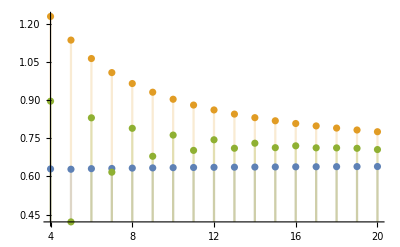

```mathematica
(* Simplified formulas obtained by hand *)
stairs2MeanSimplified = Piecewise[{{easyPart + hardPart, Mod[n,2]==0},{(n/(n+1))(2 HarmonicNumber[n-1,2] - HarmonicNumber[(n-1)/2,2]) + 2(2n+1)/(n^2 - 1) * (HarmonicNumber[n-1] - HarmonicNumber[(n-1)/2]) - (n^3 + 15n + 8)/((n+1)^2(n-1)), Mod[n,2]==1}}]
DiscretePlot[{stairs2Mean[n], easyPart,stairs2MeanSimplified}, {n, 4, 20}]
f[n]=(2(1+n)(HarmonicNumber[n/2-1]-HarmonicNumber[n-2]))/(n.b2-1);
```

```mathematica
Disc
```

```mathematica
(4+n (4+n (-1+(-2+n) n)))/(n-1)
```

(4+n (4+n (-1+(-2+n) n)))/(-1+n)

```mathematica
FullSimplify[(4+n (4+n (-1+(-2+n) n)))/(-1+n)]
```

2+6/(-1+n)+(-2+n) n (1+n)

```mathematica
easyPart =1/(6 (-1+n)^2 n (1+n))(-6 (4+n (4+n (-1+(-2+n) n)))+6 n^2 (-1+n^2)  (2 *HarmonicNumber[n-1,2]- HarmonicNumber[n/2,2]))
```

(-6 (4+n (4+n (-1+(-2+n) n)))+6 n^2 (-1+n^2) (2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2]))/(6 (-1+n)^2 n (1+n))

(2 (1+n) (HarmonicNumber[-1+n/2]-HarmonicNumber[-2+n]))/(-1+n^2)

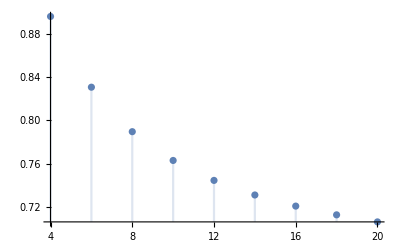

```mathematica
hardPart =(2(1+n)(HarmonicNumber[n/2-1]-HarmonicNumber[n-2]))/(n^2-1)
DiscretePlot[easyPart + hardPart, {n, 4, 20, 2}]
```

```mathematica
hardPart
```

(2 (1+n) (HarmonicNumber[-1+n/2]-HarmonicNumber[-2+n]))/(-1+n.b2)

```mathematica
Table[(2 (1+n) (HarmonicNumber[-1+n/2]-HarmonicNumber[-2+n]))/(-1+n.b2),{n,1,20}]
```

{ComplexInfinity,0,(8 (-1+HarmonicNumber[1/2]))/(-1+n.b2),-5/(-1+n.b2),(12 (-11/6+HarmonicNumber[3/2]))/(-1+n.b2),-49/(6 (-1+n.b2)),(16 (-137/60+HarmonicNumber[5/2]))/(-1+n.b2),-111/(10 (-1+n.b2)),(20 (-363/140+HarmonicNumber[7/2]))/(-1+n.b2),-5863/(420 (-1+n.b2)),(24 (-7129/2520+HarmonicNumber[9/2]))/(-1+n.b2),-21151/(1260 (-1+n.b2)),(28 (-83711/27720+HarmonicNumber[11/2]))/(-1+n.b2),-18107/(924 (-1+n.b2)),(32 (-1145993/360360+HarmonicNumber[13/2]))/(-1+n.b2),-4035307/(180180 (-1+n.b2)),(36 (-1195757/360360+HarmonicNumber[15/2]))/(-1+n.b2),-1815431/(72072 (-1+n.b2)),(40 (-42142223/12252240+HarmonicNumber[17/2]))/(-1+n.b2),-1632341/(58344 (-1+n.b2))}

```mathematica
FullSimplify[easyPart]
```

(-4+n (-4+n+2 n^2-n^3)+n^2 (-1+n^2) (2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2]))/((-1+n)^2 n (1+n))

```mathematica
Expand[easyPart]
```

-4/((-1+n)^2 (1+n))-4/((-1+n)^2 n (1+n))+n/((-1+n)^2 (1+n))+(2 n^2)/((-1+n)^2 (1+n))-n^3/((-1+n)^2 (1+n))-(2 n HarmonicNumber[-1+n,2])/((-1+n)^2 (1+n))+(2 n^3 HarmonicNumber[-1+n,2])/((-1+n)^2 (1+n))+(n HarmonicNumber[n/2,2])/((-1+n)^2 (1+n))-(n^3 HarmonicNumber[n/2,2])/((-1+n)^2 (1+n))

```mathematica
Simplify[%249]
```

(-4-4 n+n^2+2 n^3-n^4+2 n^2 (-1+n^2) HarmonicNumber[-1+n,2]+(n^2-n^4) HarmonicNumber[n/2,2])/((-1+n)^2 n (1+n))

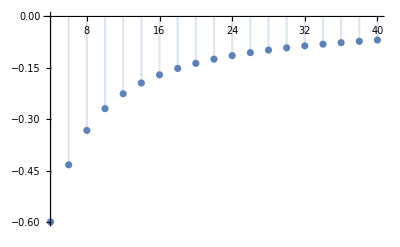

```mathematica
DiscretePlot[{stairs2Mean[n]-easyPart}, {n, 4, 40,2}]
```

```mathematica
values = Table[{n, stairs2Mean[n] - easyPart}, {n, 4, 40, 2}]
```

{{4,-3/5},{6,-13/30},{8,-629/1890},{10,-533/1980},{12,-8135/36036},{14,-525103/2702700},{16,-13963/81900},{18,-3535313/23279256},{20,-66925981/488864376},{22,-155685007/1249320072},{24,-1093322209/9561123000},{26,-190908336823/1807052247000},{28,-18051406831/183875491800},{30,-472841109539/5157269746200},{32,-225175759291/2618306178840},{34,-13981692518567/172656421938000},{36,-146000818715513/1908189806094000},{38,-98115155543129/1353080044321200},{40,-3634060848592973/52736712344716400}}

```mathematica
hardPart = FindSequenceFunction[values]
```

1/((-1+#1) (1+#1))(-10+5 EulerGamma+5 PolyGamma[0,3/2]-5 PolyGamma[0,1/2+1/2 (-2+#1)]+5 PolyGamma[0,1+1/2 (-2+#1)]-4 (-2+#1)+2 EulerGamma (-2+#1)+2 PolyGamma[0,3/2] (-2+#1)-2 PolyGamma[0,1/2+1/2 (-2+#1)] (-2+#1)+2 PolyGamma[0,1+1/2 (-2+#1)] (-2+#1))&

```mathematica
hardPart = FindSequenceFunction[values]
```

(Log[4] (-1-2 #1)+PolyGamma[0,-1/2+#1/2] (-1-2 #1)+PolyGamma[0,#1/2] (1+2 #1))/((-1+#1) (1+#1))&

```mathematica
DiscretePlot[hardPart, {n, 4, 40}]
```

-Graphics-

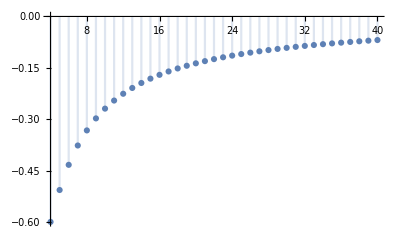

(21 (25/12-EulerGamma-Log[4]-PolyGamma[0,9/2]))/(-1+n.b2)

```mathematica
fun[n_]:=((1+2n)(PolyGamma[0,n/2]-PolyGamma[0,n/2-1/2]-Log[4]))/(n^2-1)
DiscretePlot[N[fun[n]], {n, 4, 40}]
```

```mathematica
Simplify[(21 (25/12-EulerGamma-Log[4]-PolyGamma[0,9/2]))/(-1+n.b2)]
```

-(7 (-25+12 EulerGamma+12 Log[4]+12 PolyGamma[0,9/2]))/(4 (-1+n.b2))

```mathematica
N[fun[10]]
```

-26.65/(-1.+n.b2)

```mathematica
hardPart2 = FullSimplify[stairs2Mean[n] -easyPart, Assumptions->{n > 3 && Mod[n,2]== 0 && n∈Integers}]
```

(2 (1+2 n) (-HarmonicNumber[1-n]+HarmonicNumber[-n/2]))/(-1+n^2)

```mathematica
Table[hardPart2,{n,1,20}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate}

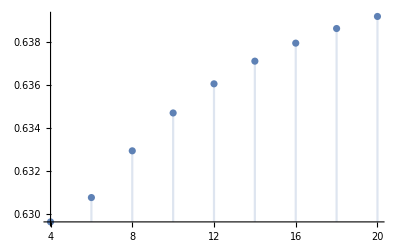

```mathematica
hardPart = (2 (1+2 n) (HarmonicNumber[n-1]-HarmonicNumber[n/2]))/(-1+n^2)-2(1 + 2n)/(n(n+1));
DiscretePlot[{stairs2Mean[n], easyPart +hardPart2}, {n, 4, 20, 2}]
```

```mathematica
DiscretePlot[{hardPart2}, {n, 4, 20,2}]
```

-Graphics-

```mathematica
Simplify[easyPart + hardPart]
```

-(2+4 n)/(n+n^2)+(2 (1+2 n) (HarmonicNumber[-1+n]-HarmonicNumber[n/2]))/(-1+n^2)+1/(6 (-1+n)^2 n (1+n))(-6 (4+n (4+n (-1+(-2+n) n)))+6 n^2 (-1+n^2) (2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2]))

```mathematica
simpHarmonic[1/(6 (-1+n^2)^2)(1+n) (-6 (2+n (5+(-2+n) n))+n (-1+n^2) π^2+12 (1+n-2 n^2) PolyGamma[0,2-n]+6 (-1+n) ((2+4 n) PolyGamma[0,1/2-n/2]+n (1+n) (-2 PolyGamma[1,n]+PolyGamma[1,(1+n)/2])))]
```

1/(6 (-1+n)^2 (1+n))(-12-6 n (5+(-2+n) n)+n (-1+n^2) π^2+12 (-1+n) (1+2 n) HarmonicNumber[1/2 (-1-n)]+12 (1+n-2 n^2) HarmonicNumber[1-n]+6 (-1+n) n (1+n) (-2 PolyGamma[1,n]+PolyGamma[1,(1+n)/2]))

```mathematica
2n^2 - n - 1
```

-1-n+2 n^2

```mathematica
FullSimplify[-1-n+2 n^2]
```

(-1+n) (1+2 n)

```mathematica
-6 (2+n (5+(-2+n) n))
```

-6 (2+n (5+(-2+n) n))

```mathematica
Expand[%254]
```

-12-30 n+12 n^2-6 n^3

```mathematica
Simplify[-12-30 n+12 n^2-6 n^3]
```

-6 (2+5 n-2 n^2+n^3)

```mathematica
-(n^3 - 2n^2 + 5n + 2)/(n^2 - 1)/(n-1) + 2(2n+1)/(n^2 - 1) * (1/(n-1) - 4/(n+1))
```

(-2-5 n+2 n^2-n^3)/((-1+n) (-1+n^2))+(2 (1+2 n) (1/(-1+n)-4/(1+n)))/(-1+n^2)

```mathematica
Simplify[(-2-5 n+2 n^2-n^3)/((-1+n) (-1+n^2))+(2 (1+2 n) (1/(-1+n)-4/(1+n)))/(-1+n^2)]
```

-(8+15 n+n^3)/((-1+n) (1+n)^2)

```mathematica
expr2=1/((-1+n)^2 n (1+n))(-4+n (-4+n+2 n^2-n^3)+n^2 (-1+n^2) (2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2])) + 2(2n+1)/(n+1) * ((HarmonicNumber[n-1] - HarmonicNumber[n/2])/(n-1) - 1/n)
```

(2 (1+2 n) (-1/n+(HarmonicNumber[-1+n]-HarmonicNumber[n/2])/(-1+n)))/(1+n)+(-4+n (-4+n+2 n^2-n^3)+n^2 (-1+n^2) (2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2]))/((-1+n)^2 n (1+n))

```mathematica
Expand[(-4+n (-4+n+2 n^2-n^3))/((-1+n)^2 n (1+n))]
```

-4/((-1+n)^2 (1+n))-4/((-1+n)^2 n (1+n))+n/((-1+n)^2 (1+n))+(2 n^2)/((-1+n)^2 (1+n))-n^3/((-1+n)^2 (1+n))

```mathematica
Simplify[-4/((-1+n)^2 (1+n))-4/((-1+n)^2 n (1+n))+n/((-1+n)^2 (1+n))+(2 n^2)/((-1+n)^2 (1+n))-n^3/((-1+n)^2 (1+n))]
```

(-4-4 n+n^2+2 n^3-n^4)/((-1+n)^2 n (1+n))

```mathematica
Simplify[(n^2 (-1+n^2))/((-1+n)^2 n (1+n))]
```

n/(-1+n)

```mathematica
( 2(2n+1)/(n+1) )* (1/(n-1)) * 1/((-1+n)^2 n (1+n))
```

(2 (1+2 n))/((-1+n)^3 n (1+n)^2)

```mathematica
Simplify[(2 (1+2 n))/((-1+n)^3 n (1+n)^2)]
```

(2+4 n)/((-1+n)^3 n (1+n)^2)

```mathematica
2(2n+1)/(n+1) /n *  1/((-1+n)^2 n (1+n)) + Out[268]
```

-4/((-1+n)^2 (1+n))-4/((-1+n)^2 n (1+n))+n/((-1+n)^2 (1+n))+(2 n^2)/((-1+n)^2 (1+n))-n^3/((-1+n)^2 (1+n))+(2 (1+2 n))/((-1+n)^2 n^2 (1+n)^2)

```mathematica
Simplify[-4/((-1+n)^2 (1+n))-4/((-1+n)^2 n (1+n))+n/((-1+n)^2 (1+n))+(2 n^2)/((-1+n)^2 (1+n))-n^3/((-1+n)^2 (1+n))+(2 (1+2 n))/((-1+n)^2 n^2 (1+n)^2)]
```

(2-8 n^2-3 n^3+3 n^4+n^5-n^6)/(n^2 (-1+n^2)^2)

(2-8 n^2-3 n^3+3 n^4+n^5-n^6)/(n^2 (-1+n^2)^2)+(2 (1+2 n) (HarmonicNumber[-1+n]-HarmonicNumber[n/2]))/((-1+n)^3 n (1+n)^2)+(n (2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2]))/(-1+n)

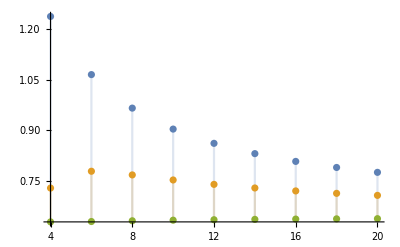

```mathematica
expr = (2-8 n^2-3 n^3+3 n^4+n^5-n^6)/(n^2 (-1+n^2)^2) + n/(-1+n)(2 HarmonicNumber[-1+n,2]-HarmonicNumber[n/2,2]) + (2 (1+2 n))/((-1+n)^3 n (1+n)^2)(HarmonicNumber[n-1] - HarmonicNumber[n/2])
DiscretePlot[{expr, expr2,stairs2Mean[n]}, {n, 4, 20, 2}]
```

```mathematica
{n>3,n∈Integers};
```

Trying to figure out how to simplify the stairs2 mean; breaking up the sum further

```mathematica
part1EvenN [n_]:= Simplify[Sum[2n /(2i(2i+1)(2i -1)) + 2i/((n-i)(n-1)), {i, 1, n/2 - 1} ],Assumptions->{n>3,n∈Integers, Mod[n,2]==0}]
result = part1EvenN[n]
```

1/(-1+n)(n (2+EulerGamma-n-EulerGamma n+PolyGamma[0,1/2]-n PolyGamma[0,1/2]+(-1+n) PolyGamma[0,1/2 (-1+n)]-(-1+n) PolyGamma[0,n/2])-2 [n/2])

```mathematica
simpHarmonic=FullSimplify[#,ComplexityFunction->(LeafCount[#]+100Count[#,_PolyGamma,All]&)]&;
simplified =simpHarmonic[result]
```

(-((-2+n) n)+(-1+n) n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[1/2 (-2+n)]+Log[4])-2 [n/2])/(-1+n)

```mathematica
easyPart = (-((-2+n) n)+(-1+n) n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[1/2 (-2+n)]+Log[4]))/(-1+n);
```

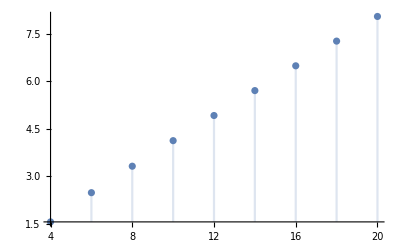

```mathematica
DiscretePlot[simplified, {n, 4, 20,2}]
```

```mathematica
Clear[f,n];
f [k_]:=[k] /.{n-> 2k}
```

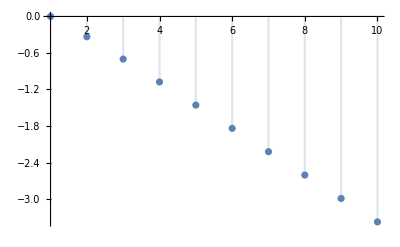

```mathematica
DiscretePlot[f[k], {k, 1, 10}]
```

```mathematica
values = Table[{k, f[k]}, {k, 1, 15}]
```

{{1,0},{2,-1/3},{3,-7/10},{4,-113/105},{5,-367/252},{6,-4247/2310},{7,-57191/25740},{8,-23477/9009},{9,-407117/136136},{10,-39288727/11639628},{11,-39792607/10581480},{12,-924929651/223092870},{13,-4665834631/1029659400},{14,-14103738593/2868336900},{15,-58812219091/11090902680}}

```mathematica
diffRoot =FindSequenceFunction[values]
```

-#1+EulerGamma #1+PolyGamma[0,3/2] #1-PolyGamma[0,1/2+#1] #1+PolyGamma[0,1+#1] #1&

```mathematica
g[k_]:=-k + EulerGamma k + PolyGamma[0, 3/2] k - PolyGamma[0, 1/2 + k] k + PolyGamma[0, 1 + k] k;
DiscretePlot[N[g[k]], {k, 1, 10}]
```

-Graphics-

```mathematica
simpHarmonic[g[n/2]]
```

-1/2 n (-1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[n/2]+Log[4])

```mathematica
hardPart = -2 * simpHarmonic[g[n/2]] / (n-1);
simplifiedVersion = easyPart + hardPart
```

(n (-1+HarmonicNumber[1/2 (-1+n)]-HarmonicNumber[n/2]+Log[4]))/(-1+n)+(-((-2+n) n)+(-1+n) n (HarmonicNumber[1/2 (-3+n)]-HarmonicNumber[1/2 (-2+n)]+Log[4]))/(-1+n)

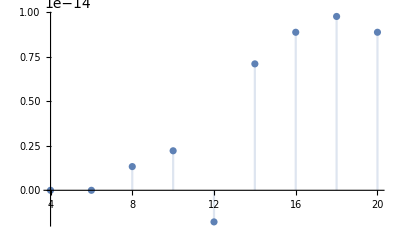

```mathematica
DiscretePlot[{part1EvenN[n]-(simplifiedVersion)}, {n, 4, 20, 2}]
```

```mathematica
FullSimplify[part1EvenN[n] == easyPart + hardPart, Assumptions->{n>3,n∈Integers, Mod[n,2]==0}]
```

2+(-1+n) n (HarmonicNumber[1/2 (-3+n)]-2 HarmonicNumber[-n]-HarmonicNumber[n/2]+Log[4])+2 (-1+n) n (EulerGamma+PolyGamma[0,-n/2])==0

```mathematica
Reduce[2+(-1+n) n (HarmonicNumber[1/2 (-3+n)]-2 HarmonicNumber[-n]-HarmonicNumber[n/2]+Log[4])+2 (-1+n) n (EulerGamma+PolyGamma[0,-n/2])==0]
```

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

False

```mathematica
2+(-1+n) n (HarmonicNumber[1/2 (-3+n)]-2 HarmonicNumber[-n]-HarmonicNumber[n/2]+Log[4])+2 (-1+n) n (EulerGamma+PolyGamma[0,-n/2])
```

2+(-1+n) n (HarmonicNumber[1/2 (-3+n)]-2 HarmonicNumber[-n]-HarmonicNumber[n/2]+Log[4])+2 (-1+n) n (EulerGamma+PolyGamma[0,-n/2])

```mathematica
part2EvenN[n_]:= Sum[i * Sum[1/(j(i+j)(i+j+1)(i+j-1)), {j, i+1, n-i-1}], {i, 1, n/2 - 1}]
part2EvenN[n]
```

(6+n (31-2 π^2)+n^2 (-19+2 π^2)-12 (-1+n) n PolyGamma[1,-1+n])/(24 (-1+n) n)+1/(8 (-2+n) (-1+n) n)(16-34 n+4 EulerGamma n+31 n^2-6 EulerGamma n^2-5 n^3+2 EulerGamma n^3+4 n PolyGamma[0,5/2]-6 n^2 PolyGamma[0,5/2]+2 n^3 PolyGamma[0,5/2]-8 PolyGamma[0,3-n]+20 n PolyGamma[0,3-n]-8 n^2 PolyGamma[0,3-n]+8 PolyGamma[0,1-n/2]-20 n PolyGamma[0,1-n/2]+8 n^2 PolyGamma[0,1-n/2]+8 PolyGamma[0,-1+n/2]-16 n PolyGamma[0,-1+n/2]+2 n^2 PolyGamma[0,-1+n/2]+2 n^3 PolyGamma[0,-1+n/2]-4 n PolyGamma[0,1/2+n/2]+6 n^2 PolyGamma[0,1/2+n/2]-2 n^3 PolyGamma[0,1/2+n/2]+12 n PolyGamma[0,-2+n]-18 n^2 PolyGamma[0,-2+n]+6 n^3 PolyGamma[0,-2+n]+16 PolyGamma[0,-1+n]-44 n PolyGamma[0,-1+n]+34 n^2 PolyGamma[0,-1+n]-6 n^3 PolyGamma[0,-1+n]-24 PolyGamma[0,n/2]+52 n PolyGamma[0,n/2]-24 n^2 PolyGamma[0,n/2]-32 n [n/2]+48 n^2 [n/2]-16 n^3 [n/2]-16 n [n/2]+24 n^2 [n/2]-8 n^3 [n/2]+16 n [n/2]-24 n^2 [n/2]+8 n^3 [n/2]+32 n [n/2]-48 n^2 [n/2]+16 n^3 [n/2])

```mathematica
Factor[Out[2]]
```

1/(12 (-2+n) (-1+n) n)(18-79 n+6 EulerGamma n+81 n^2-9 EulerGamma n^2-17 n^3+3 EulerGamma n^3+2 n π^2-3 n^2 π^2+n^3 π^2+6 n PolyGamma[0,5/2]-9 n^2 PolyGamma[0,5/2]+3 n^3 PolyGamma[0,5/2]-12 PolyGamma[0,3-n]+30 n PolyGamma[0,3-n]-12 n^2 PolyGamma[0,3-n]+12 PolyGamma[0,1-n/2]-30 n PolyGamma[0,1-n/2]+12 n^2 PolyGamma[0,1-n/2]+12 PolyGamma[0,-1+n/2]-24 n PolyGamma[0,-1+n/2]+3 n^2 PolyGamma[0,-1+n/2]+3 n^3 PolyGamma[0,-1+n/2]-6 n PolyGamma[0,1/2+n/2]+9 n^2 PolyGamma[0,1/2+n/2]-3 n^3 PolyGamma[0,1/2+n/2]+18 n PolyGamma[0,-2+n]-27 n^2 PolyGamma[0,-2+n]+9 n^3 PolyGamma[0,-2+n]+24 PolyGamma[0,-1+n]-66 n PolyGamma[0,-1+n]+51 n^2 PolyGamma[0,-1+n]-9 n^3 PolyGamma[0,-1+n]-36 PolyGamma[0,n/2]+78 n PolyGamma[0,n/2]-36 n^2 PolyGamma[0,n/2]-12 n PolyGamma[1,-1+n]+18 n^2 PolyGamma[1,-1+n]-6 n^3 PolyGamma[1,-1+n]-48 n [n/2]+72 n^2 [n/2]-24 n^3 [n/2]-24 n [n/2]+36 n^2 [n/2]-12 n^3 [n/2]+24 n [n/2]-36 n^2 [n/2]+12 n^3 [n/2]+48 n [n/2]-72 n^2 [n/2]+24 n^3 [n/2])

```mathematica
Simplify[Out[3]]
```

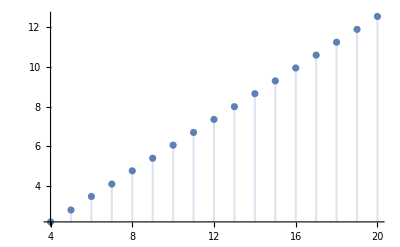

```mathematica
stairs2[n_,i_,j_]:= i/j;
stairs2MeanNaive[n_]:= MeanDaughterStatistic[stairs2, n]
DiscretePlot[stairs2MeanNaive[n], {n, 4, 20}]
```

```mathematica
evenVals = Table[{n, stairs2MeanNaive[n]}, {n, 4, 40, 2}]
```

{{4,20/9},{6,1049/300},{8,11713/2450},{10,1926703/317520},{12,235525357/32016600},{14,40095526123/4637833200},{16,80631220403/8116208100},{18,46803493968059/4169927361600},{20,5651195567280253/451603133261280},{22,1133383045395677/82109660592960},{24,66771958631919539/4424038101763280},{26,75265427450594884717/4594193413369560000},{28,2035570971343322988259/115182992006622540000},{30,1714398331437787613907799/90410969859064919064000},{32,3299252039297262817827160343/162909266314802601038445000},{34,6605881322394796672045927411/306652736592569601954720000},{36,6612441476885087072367621211/289616473448537957401680000},{38,9060470567612840300886129423259/375617323090466965594326240000},{40,9067706990767901904110659322119/356836456935943617314609928000}}

```mathematica
FindSequenceFunction[evenVals]
```

FindSequenceFunction[{{4,20/9},{6,1049/300},{8,11713/2450},{10,1926703/317520},{12,235525357/32016600},{14,40095526123/4637833200},{16,80631220403/8116208100},{18,46803493968059/4169927361600},{20,5651195567280253/451603133261280},{22,1133383045395677/82109660592960},{24,66771958631919539/4424038101763280},{26,75265427450594884717/4594193413369560000},{28,2035570971343322988259/115182992006622540000},{30,1714398331437787613907799/90410969859064919064000},{32,3299252039297262817827160343/162909266314802601038445000},{34,6605881322394796672045927411/306652736592569601954720000},{36,6612441476885087072367621211/289616473448537957401680000},{38,9060470567612840300886129423259/375617323090466965594326240000},{40,9067706990767901904110659322119/356836456935943617314609928000}}]